```mathematica
f[t_]=E^(-γ t)A Cos[ω1 t - α]
```

A ⅇ^(-t γ) Cos[α-t ω1]

```mathematica
α/.Simplify[Solve[D[f[x],x]==0,α]]/.ω1->0
```

{-π/2,π/2,-π/2,π/2}

```mathematica
Clear[ζ,ω0]
sol=Simplify[DSolve[{x''[t]+x'[t]2 ω0 ζ+ω0^2 x[t]==0,x[0]==1,x'[0]==0},x,t]];
Simplify[x[t]/.sol,{ω0>0,ζ>0,t>0}]
```

{1/(2 (-1+ζ^2))ⅇ^(-t (ζ+√(-1+ζ^2)) ω0) (-1+ζ^2-ζ √(-1+ζ^2)+ⅇ^(2 t √(-1+ζ^2) ω0) (-1+ζ^2+ζ √(-1+ζ^2)))}

```mathematica
Simplify[D[(a x^3 + b x^2/.Solve[ei d == a l^3+b l^2&&ei Sin[θ]==3 a l^2+2 b l,{a,b}]),{x,2}]]/.x->l
Simplify[D[(a x^3 + b x^2/.Solve[ei d == a l^3+b l^2&&ei Sin[θ]==3 a l^2+2 b l,{a,b}]),{x,2}]]/.x->0
```

{(2 ei (-3 d l+2 l^2 Sin[θ]))/l^3}

{(2 ei (3 d l-l^2 Sin[θ]))/l^3}

```mathematica
f[x_]=(a x^3+b x^2+c x +d)/ei;
sol=Solve[{(D[f[x],{x,1}]/.x->l)==Sin[θ2],(D[f[x],{x,1}]/.x->0)==Sin[θ1],
f[0]==0,f[l]==0},{a,b,c,d}];
(* Torque *)
Simplify[-D[f[x] e l^4,{x,2}]/.sol[[1]]/.x->{0,l}]
(* shear force *)
Simplify[-D[f[x] e l^4,{x,3}]/.sol[[1]]]
```

{2 e l^3 (2 Sin[θ1]+Sin[θ2]),-2 e l^3 (Sin[θ1]+2 Sin[θ2])}

-6 e l^2 (Sin[θ1]+Sin[θ2])

```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{x}, {y}})/.θ->π/2
```

{{-y},{x}}

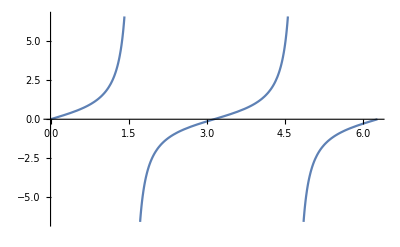

```mathematica
Plot[Tan[θ+π],{θ,0,2π}]
```